# Fit lineare dei dati Metodo dei Minimi Quadrati Riccardo Finotello

# Istruzioni

Il presente foglio di calcolo di Mathematica permette di calcolare un fit lineare dei dati inseriti da un file .dat contenente quattro colonne in cui siano inseriti, nell’ordine, ascisse, ordinate, errore sulle ascisse (eventualmente nullo), errore sulle ordinate.
L’analisi si svolge in tre passi: nel primo si analizzano e si rappresentano i dati così come sono, stimando un primo fit; nel secondo viene riportato l’errore dalle ascisse alle ordinate utilizzando il precedente fit; infine (potrebbe non essere necessario) si ristima un fit utilizzando informazioni derivanti dall’analisi dell’errore a posteriore.
Il file di input può contenere anche un’eventuale riga di intestazione dei dati, che verrà automaticamente ignorata dal programma.
Dopo aver inserito i dati nella sezione “Input dei dati” è sufficiente dare il comando “Evaluate Notebook” dal menù “Evaluation”. Il risultato dell’analisi viene salvato in file all’interno della cartella “Documenti”, recanti il nome dell’analisi (viene creata una cartella dal nome dell’esperienza). E’ possibile far eseguire più di un’analisi all’interno della stessa esperienza, posto di cambiare il nome del fit relativo (cioè il nome della sottocartella).

Per info:
Riccardo Finotello
riccardo.finotello@edu.unito.it

# Input dei dati

```mathematica
Clear["Global`*"] (*reset dell'intero Notebook*)
Needs["ErrorBarPlots`"](*pacchetto per barre d'errore*)
```

```mathematica
NomeEsperienza="EffettoHall";(*Nome della cartella principale ..\SpettroscopiaAlfa. Evitare gli spazi tra le parole. *)
NomeFit="1200mA";(*nome della sottocartella ..\SpettroscopiaAlfa\NomeFit. Evitare gli spazi tra le parole. *)
InputFile="Desktop\\1200mA.dat";(*Inserire il path del file: doppia barra \\ per separare i file oppure singola /*)
EtichettaAscissa="I" ;
UnitàMisuraAscissa="mA";(*inserire il carattere _ oppure Blank[] se non specificata*)
EtichettaOrdinata="V";
UnitàMisuraOrdinata="mV";(*inserire il carattere _ oppure Blank[] se non specificata*)
```

# Analisi dei dati

### Input del file indicato

```mathematica
inputData=Import[InputFile,"Data"];
Grid[inputData]
```

-8.04 | -14.31 | 0.02 | 0.02
-6.9 | -12.35 | 0.02 | 0.02
-6. | -10.84 | 0.02 | 0.02
-5.56 | -9.93 | 0.02 | 0.02
-5.03 | -8.95 | 0.02 | 0.02
-3.85 | -6.85 | 0.02 | 0.02
-2.9 | -5.17 | 0.02 | 0.02
-1.91 | -3.41 | 0.02 | 0.02
-0.92 | -1.71 | 0.02 | 0.02
-0.47 | -0.85 | 0.02 | 0.02
0. | 0. | 0.02 | 0.02
0.48 | 0.79 | 0.02 | 0.02
0.9 | 1.53 | 0.02 | 0.02
1.96 | 3.45 | 0.02 | 0.02
2.89 | 5.24 | 0.02 | 0.02
3.93 | 7.13 | 0.02 | 0.02
5.03 | 8.98 | 0.02 | 0.02
5.5 | 9.96 | 0.02 | 0.02
6.05 | 10.87 | 0.02 | 0.02
7.01 | 12.65 | 0.02 | 0.02
8.01 | 14.29 | 0.02 | 0.02

### Costruzione liste di ascisse, ordinate ed errori

```mathematica
If[StringQ[inputData[[1,1]]],ascissa=Drop[Flatten[inputData[[All,1]]],1],ascissa=Flatten[inputData[[All,1]]]];
If[StringQ[inputData[[1,2]]],ordinata=Drop[Flatten[inputData[[All,2]]],1],ordinata=Flatten[inputData[[All,2]]]];
If[StringQ[inputData[[1,3]]],sigmaAscissa=Drop[Flatten[inputData[[All,3]]],1],sigmaAscissa=Flatten[inputData[[All,3]]]];
If[StringQ[inputData[[1,4]]],sigmaOrdinata=Drop[Flatten[inputData[[All,4]]],1],sigmaOrdinata=Flatten[inputData[[All,4]]]];
Lungh=Length[ascissa];
```

```mathematica
TopLimit=50;
If[Lungh≤TopLimit,Print["x = ",ascissa],"Liste troppo lunghe per essere visualizzate"]
If[Lungh≤TopLimit,Print["y = ",ordinata],"Liste troppo lunghe per essere visualizzate"]
If[Lungh≤TopLimit,Print["σ_x = ",sigmaAscissa],"Liste troppo lunghe per essere visualizzate"]
If[Lungh≤TopLimit,Print["σ_y = ",sigmaOrdinata],"Liste troppo lunghe per essere visualizzate"]
```

x = {-8.04,-6.9,-6.,-5.56,-5.03,-3.85,-2.9,-1.91,-0.92,-0.47,0.,0.48,0.9,1.96,2.89,3.93,5.03,5.5,6.05,7.01,8.01}

y = {-14.31,-12.35,-10.84,-9.93,-8.95,-6.85,-5.17,-3.41,-1.71,-0.85,0.,0.79,1.53,3.45,5.24,7.13,8.98,9.96,10.87,12.65,14.29}

σ_x = {0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02}

σ_y = {0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02}

### Controllo dei dati

```mathematica
If[Lungh==Length[ordinata]&&Lungh==Length[sigmaAscissa]&&Lungh==Length[sigmaOrdinata],"Le liste sono consistenti","Errore: controllare l'input"]
```

Le liste sono consistenti

### Calcolo del ChiQuadrato (Esp1 - Prof. Balestra)

```mathematica
matD={{Sum[1/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[ascissa[[i]]/(sigmaOrdinata[[i]])^2,{i,Lungh}]},{Sum[ascissa[[i]]/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^2/(sigmaOrdinata[[i]])^2,{i,Lungh}]}};
matDinver=Inverse[matD];
matB ={Sum[ordinata[[i]]/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[((ascissa[[i]])*ordinata[[i]])/(sigmaOrdinata[[i]])^2,{i,Lungh}]};
matA = matDinver. matB;
Print["D = ",MatrixForm[matD]]
Print["D^-1 = ",MatrixForm[matDinver]]
Print["B = ",MatrixForm[matB]]
Print["A = ",MatrixForm[matA]]
```

D = (52500. | 450.
450. | 1.16637×10^6)

D^-1 = (0.0000190477 | -7.34885×10^-9
-7.34885×10^-9 | 8.57366×10^-7)

B = (1300.
2.08981×10^6)

A = (0.0094043
1.79172)

### Creazione dei grafici

```mathematica
dati=Table[{ascissa[[i]],ordinata[[i]]},{i,Lungh}];
If[Lungh≤TopLimit,Grid[dati],"Griglia troppo lunga per essere visualizzata"]
```

-8.04 | -14.31
-6.9 | -12.35
-6. | -10.84
-5.56 | -9.93
-5.03 | -8.95
-3.85 | -6.85
-2.9 | -5.17
-1.91 | -3.41
-0.92 | -1.71
-0.47 | -0.85
0. | 0.
0.48 | 0.79
0.9 | 1.53
1.96 | 3.45
2.89 | 5.24
3.93 | 7.13
5.03 | 8.98
5.5 | 9.96
6.05 | 10.87
7.01 | 12.65
8.01 | 14.29

```mathematica
err=Table[{dati[[i]],ErrorBar[sigmaAscissa[[i]],sigmaOrdinata[[i]]]},{i,Lungh}];
If[Lungh≤TopLimit,Grid[err],"Griglia troppo lunga per essere visualizzata"]
```

{-8.04,-14.31} | ErrorBar[0.02,0.02]
{-6.9,-12.35} | ErrorBar[0.02,0.02]
{-6.,-10.84} | ErrorBar[0.02,0.02]
{-5.56,-9.93} | ErrorBar[0.02,0.02]
{-5.03,-8.95} | ErrorBar[0.02,0.02]
{-3.85,-6.85} | ErrorBar[0.02,0.02]
{-2.9,-5.17} | ErrorBar[0.02,0.02]
{-1.91,-3.41} | ErrorBar[0.02,0.02]
{-0.92,-1.71} | ErrorBar[0.02,0.02]
{-0.47,-0.85} | ErrorBar[0.02,0.02]
{0.,0.} | ErrorBar[0.02,0.02]
{0.48,0.79} | ErrorBar[0.02,0.02]
{0.9,1.53} | ErrorBar[0.02,0.02]
{1.96,3.45} | ErrorBar[0.02,0.02]
{2.89,5.24} | ErrorBar[0.02,0.02]
{3.93,7.13} | ErrorBar[0.02,0.02]
{5.03,8.98} | ErrorBar[0.02,0.02]
{5.5,9.96} | ErrorBar[0.02,0.02]
{6.05,10.87} | ErrorBar[0.02,0.02]
{7.01,12.65} | ErrorBar[0.02,0.02]
{8.01,14.29} | ErrorBar[0.02,0.02]

```mathematica
If[StringQ[UnitàMisuraAscissa],AscissaLabel=EtichettaAscissa<>" ["<>UnitàMisuraAscissa<>"]",AscissaLabel=EtichettaAscissa];
If[StringQ[UnitàMisuraOrdinata],OrdinataLabel=EtichettaOrdinata<>" ["<>UnitàMisuraOrdinata<>"]",OrdinataLabel=EtichettaOrdinata];
```

### Grafici e parametri del primo fit

#### Grafico dei punti sperimentali

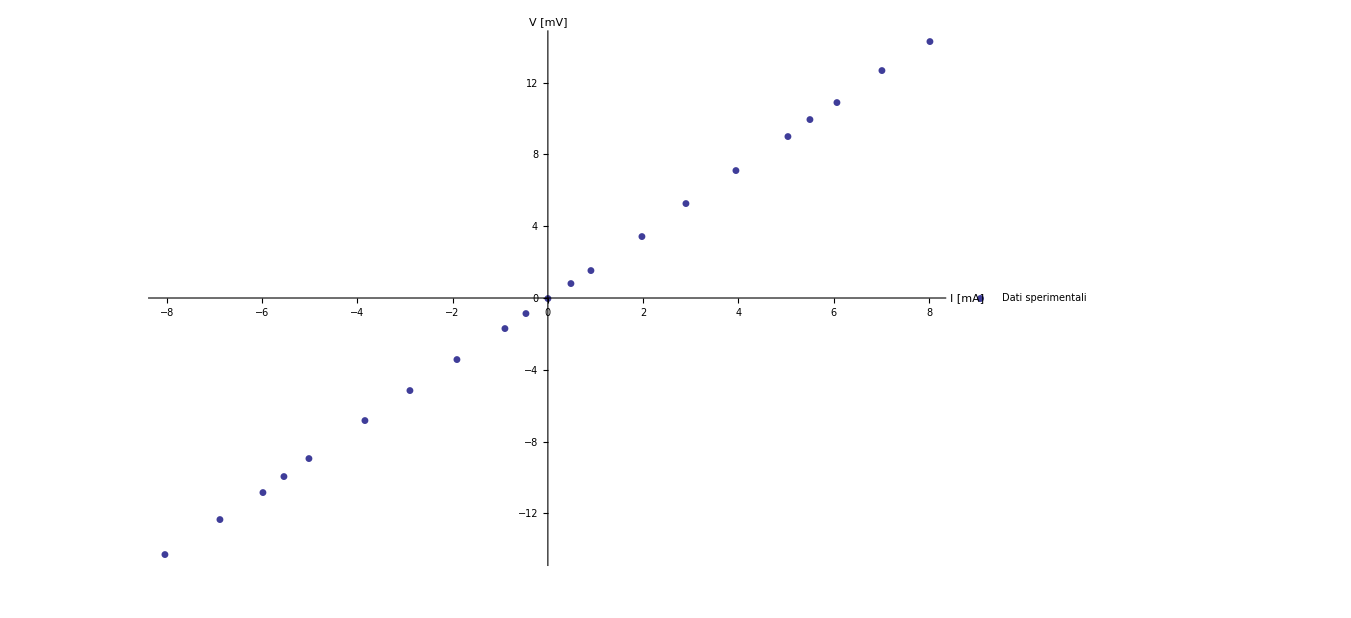

```mathematica
Grafico=ErrorListPlot[err,PlotRange->All,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Black,Bold,Large],ImageSize->1000,PlotMarkers->Automatic,PlotLegends->{"Dati sperimentali"}]
```

#### Parametri del fit lineare con il metodo dei minimi quadrati

```mathematica
a=matA[[1]];
siga=Sqrt[matDinver[[1,1]]];
b=matA[[2]];
sigb=Sqrt[matDinver[[2,2]]];
f[x_]:=a+b*x;
Print["Retta y = f(x) = a + bx"]
Print["a = (",a," ± ",siga,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]]
Print["b = (",b," ± ",sigb,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-1,""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-1,""]]]
```

Retta y = f(x) = a + bx

a = (0.0094043 ± 0.00436437)mV

StringJoin::string: String expected at position 2 in "mV" <> 1/"mA".

b = (1.79172 ± 0.000925941)mV<>1/mA

#### Grafico della retta di fit

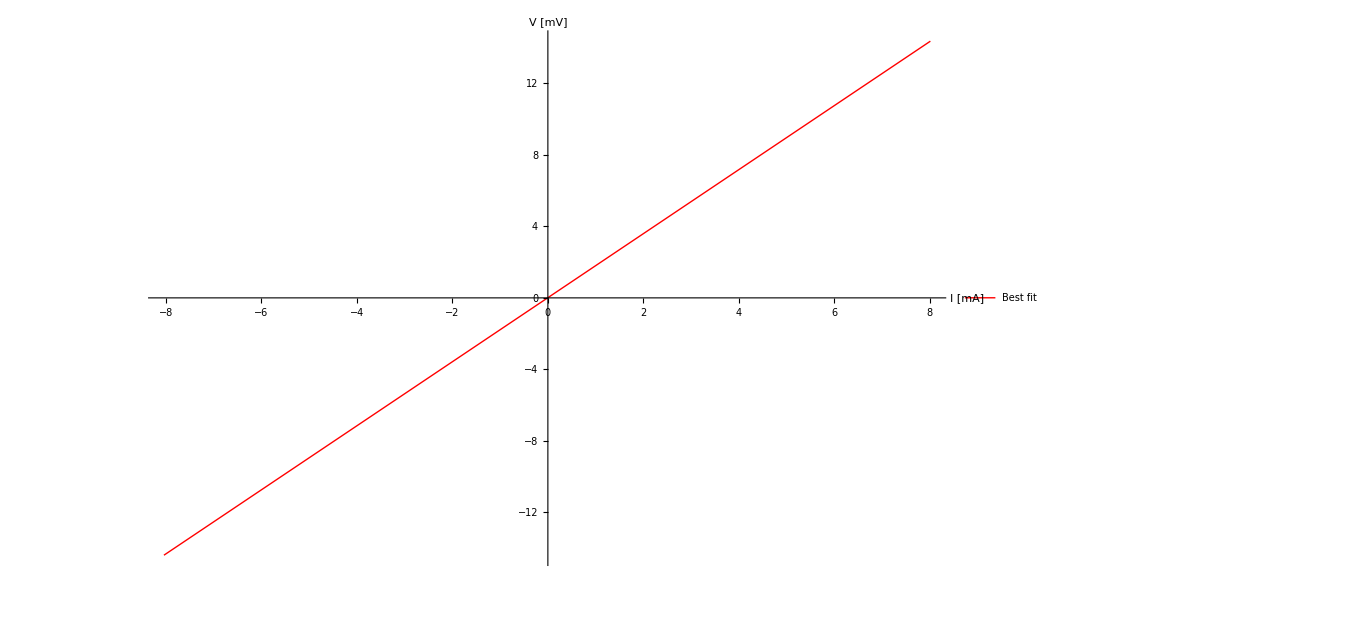

```mathematica
GraficoRetta=Plot[f[x],{x,First[ascissa],Last[ascissa]},PlotRange->All,ImageSize->1000,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Black,Bold,Large],PlotStyle->Red,PlotLegends->{"Best fit"}]
```

#### Grafico cumulativo (dati e retta)

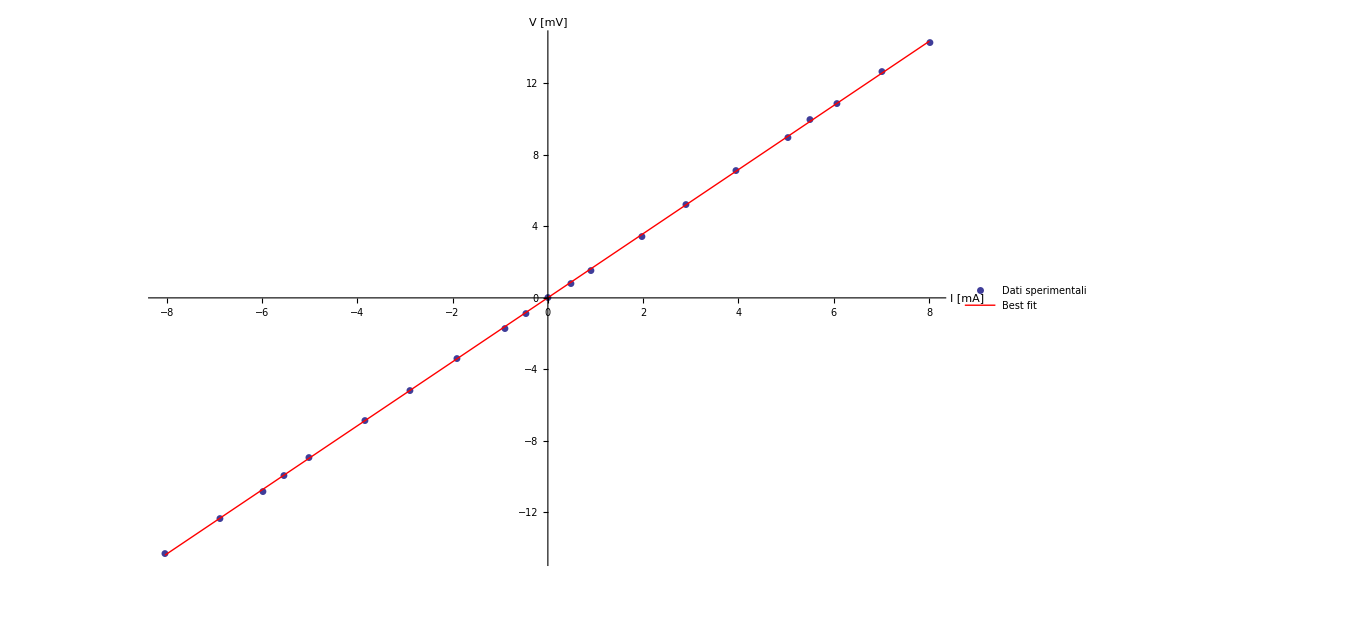

```mathematica
GraficoTot=Show[Grafico,GraficoRetta]
```

#### Parametri del Chi Quadro

```mathematica
chi2=Sum[(f[ascissa[[i]]]-ordinata[[i]])^2/sigmaOrdinata[[i]]^2,{i,Lungh}];
sy=Sqrt[Sum[(f[ascissa[[i]]]-ordinata[[i]])^2/(Lungh-2),{i,Lungh}]];
Print["Coefficiente di correlazione lineare: ρ = ",Correlation[ascissa,ordinata]]
Print["χ^2 = ",chi2]
Print["Gradi di libertà del sistema: dof = ",Lungh-2]
Print["Eventuale errore a posteriori sulle ordinate: σ_y = ",sy,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]]
```

Coefficiente di correlazione lineare: ρ = 0.999973

χ^2 = 198.941

Gradi di libertà del sistema: dof = 19

Eventuale errore a posteriori sulle ordinate: σ_y = 0.0647165mV

# Seconda analisi dei dati

Vengono riportati gli errori in ascissa sulle ordinate, utilizzando il coefficiente angolare appena trovato dal primo fit

### Nuova stima dell’errore sulle ordinate

```mathematica
sigmaOrdinataNuove=Sqrt[sigmaOrdinata^2+(sigmaAscissa*b)^2];
If[Lungh≤TopLimit,Print["σ_y^(1) = ",sigmaOrdinataNuove],"Liste troppo lunghe per essere visualizzate"]
```

σ_y^(1) = {0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379,0.0410379}

### Calcolo del ChiQuadrato (Esp1 - Prof. Balestra)

```mathematica
matD1={{Sum[1/(sigmaOrdinataNuove[[i]])^2,{i,Lungh}],Sum[ascissa[[i]]/(sigmaOrdinataNuove[[i]])^2,{i,Lungh}]},{Sum[ascissa[[i]]/(sigmaOrdinataNuove[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^2/(sigmaOrdinataNuove[[i]])^2,{i,Lungh}]}};
matD1inver=Inverse[matD1];
matB1 ={Sum[ordinata[[i]]/(sigmaOrdinataNuove[[i]])^2,{i,Lungh}],Sum[((ascissa[[i]])*ordinata[[i]])/(sigmaOrdinataNuove[[i]])^2,{i,Lungh}]};
matA1= matD1inver. matB1;
Print["D = ",MatrixForm[matD1]]
Print["D^-1 = ",MatrixForm[matD1inver]]
Print["B = ",MatrixForm[matB1]]
Print["A = ",MatrixForm[matA1]]
```

D = (12469.5 | 106.882
106.882 | 277029.)

D^-1 = (0.0000801958 | -3.09406×10^-8
-3.09406×10^-8 | 3.60974×10^-6)

B = (308.769
496360.)

A = (0.0094043
1.79172)

### Creazione dei grafici nuovi

```mathematica
err1=Table[{dati[[i]],ErrorBar[sigmaOrdinataNuove[[i]]]},{i,Lungh}];
If[Lungh≤TopLimit,Grid[err1],"Griglia troppo lunga per essere visualizzata"]
```

{-8.04,-14.31} | ErrorBar[0.0410379]
{-6.9,-12.35} | ErrorBar[0.0410379]
{-6.,-10.84} | ErrorBar[0.0410379]
{-5.56,-9.93} | ErrorBar[0.0410379]
{-5.03,-8.95} | ErrorBar[0.0410379]
{-3.85,-6.85} | ErrorBar[0.0410379]
{-2.9,-5.17} | ErrorBar[0.0410379]
{-1.91,-3.41} | ErrorBar[0.0410379]
{-0.92,-1.71} | ErrorBar[0.0410379]
{-0.47,-0.85} | ErrorBar[0.0410379]
{0.,0.} | ErrorBar[0.0410379]
{0.48,0.79} | ErrorBar[0.0410379]
{0.9,1.53} | ErrorBar[0.0410379]
{1.96,3.45} | ErrorBar[0.0410379]
{2.89,5.24} | ErrorBar[0.0410379]
{3.93,7.13} | ErrorBar[0.0410379]
{5.03,8.98} | ErrorBar[0.0410379]
{5.5,9.96} | ErrorBar[0.0410379]
{6.05,10.87} | ErrorBar[0.0410379]
{7.01,12.65} | ErrorBar[0.0410379]
{8.01,14.29} | ErrorBar[0.0410379]

### Grafici e parametri del secondo fit

#### Grafico dei punti sperimentali

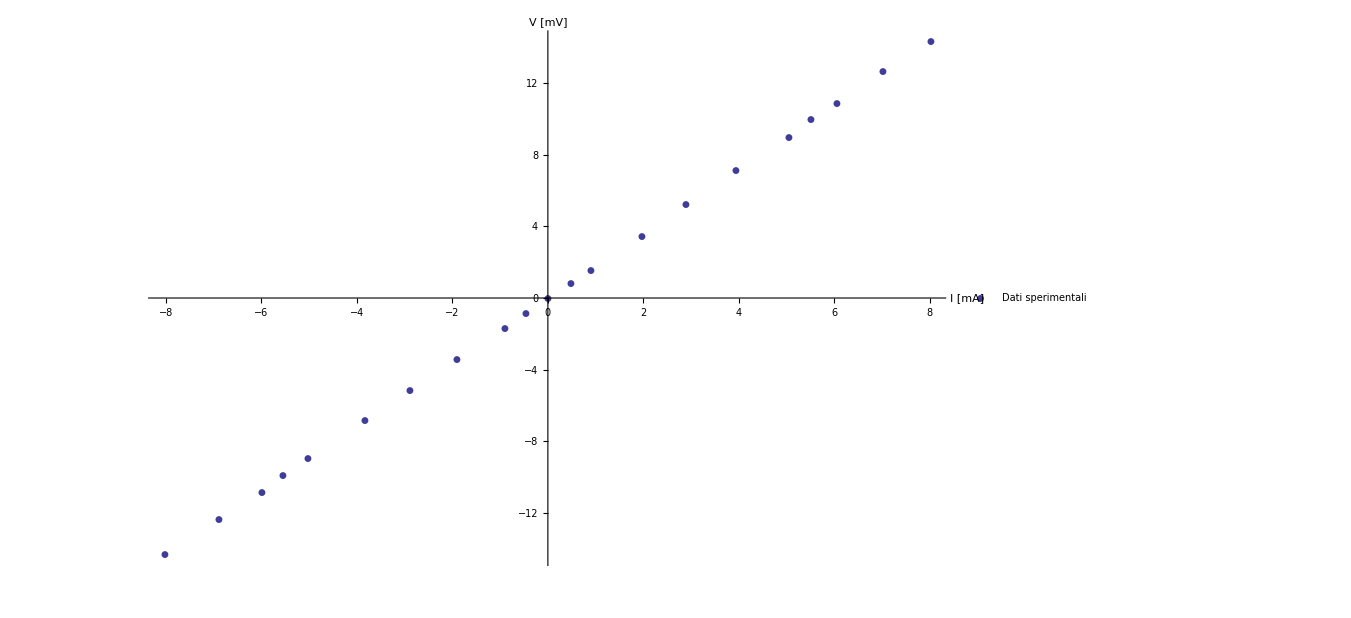

```mathematica
Grafico1=ErrorListPlot[err1,PlotRange->All,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Black,Bold,Large],ImageSize->1000,PlotMarkers->Automatic,PlotLegends->{"Dati sperimentali"}]
```

#### Parametri del fit lineare con il metodo dei minimi quadrati

```mathematica
a1=matA1[[1]];
siga1=Sqrt[matD1inver[[1,1]]];
b1=matA1[[2]];
sigb1=Sqrt[matD1inver[[2,2]]];
f1[x_]:=a1+b1*x;
Print["Retta y = f(x) = a + bx"]
Print["a = (",a1," ± ",siga1,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]]
Print["b = (",b1," ± ",sigb1,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-1,""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-1,""]]]
```

Retta y = f(x) = a + bx

a = (0.0094043 ± 0.00895521)mV

StringJoin::string: String expected at position 2 in "mV" <> 1/"mA".

b = (1.79172 ± 0.00189993)mV<>1/mA

#### Grafico della retta di fit

```mathematica
GraficoRetta1=Plot[f1[x],{x,First[ascissa],Last[ascissa]},PlotRange->All,ImageSize->1000,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Black,Bold,Large],PlotStyle->Red,PlotLegends->{"Best fit"}]
```

-Graphics-

#### Grafico cumulativo (dati e retta)

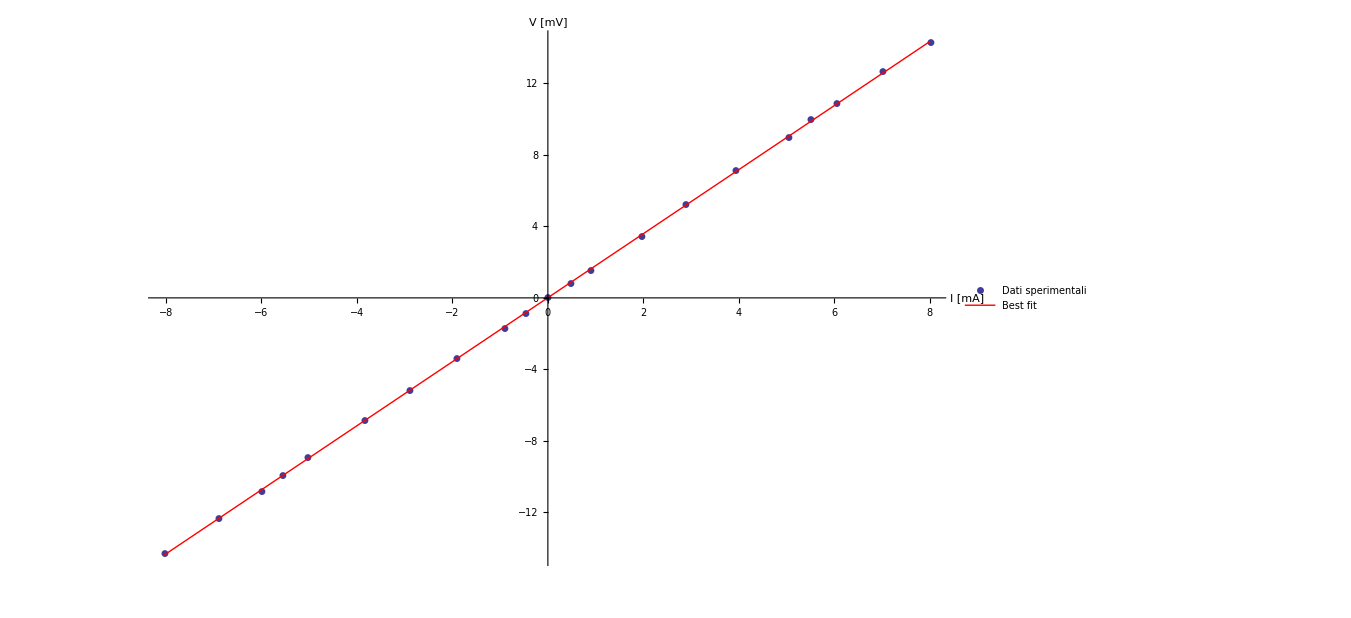

```mathematica
GraficoTot1=Show[Grafico1,GraficoRetta1]
```

#### Parametri del Chi Quadro

```mathematica
chi21=Sum[(f1[ascissa[[i]]]-ordinata[[i]])^2/sigmaOrdinataNuove[[i]]^2,{i,Lungh}];
sy1=Sqrt[Sum[(f1[ascissa[[i]]]-ordinata[[i]])^2/(Lungh-2),{i,Lungh}]];
Print["Coefficiente di correlazione lineare: ρ = ",Correlation[ascissa,ordinata]," (invariato)"]
Print["χ^2 = ",chi21]
Print["Gradi di libertà del sistema: dof = ",Lungh-2]
Print["Eventuale errore a posteriori sulle ordinate: σ_y = ",sy1,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]]
```

Coefficiente di correlazione lineare: ρ = 0.999973 (invariato)

χ^2 = 47.2513

Gradi di libertà del sistema: dof = 19

Eventuale errore a posteriori sulle ordinate: σ_y = 0.0647165mV

# Analisi dati a posteriori

Terza stima dell’errore: si utilizza l’errore a posteriori σ_y (della seconda analisi) per stimare un nuovo fit

### Nuova stima dell’errore sulle ordinate

```mathematica
sigmaOrdinataPosteriori=Table[sy1,{i,Lungh}];
If[Lungh≤TopLimit,Print["σ_y^(1) = ",sigmaOrdinataPosteriori],"Liste troppo lunghe per essere visualizzate"]
```

σ_y^(1) = {0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165,0.0647165}

### Calcolo del ChiQuadrato (Esp1 - Prof. Balestra)

```mathematica
matD2={{Sum[1/(sigmaOrdinataPosteriori[[i]])^2,{i,Lungh}],Sum[ascissa[[i]]/(sigmaOrdinataPosteriori[[i]])^2,{i,Lungh}]},{Sum[ascissa[[i]]/(sigmaOrdinataPosteriori[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^2/(sigmaOrdinataPosteriori[[i]])^2,{i,Lungh}]}};
matD2inver=Inverse[matD2];
matB2 ={Sum[ordinata[[i]]/(sigmaOrdinataPosteriori[[i]])^2,{i,Lungh}],Sum[((ascissa[[i]])*ordinata[[i]])/(sigmaOrdinataPosteriori[[i]])^2,{i,Lungh}]};
matA2= matD2inver. matB2;
Print["D = ",MatrixForm[matD2]]
Print["D^-1 = ",MatrixForm[matD2inver]]
Print["B = ",MatrixForm[matB2]]
Print["A = ",MatrixForm[matA2]]
```

D = (5014.06 | 42.9776
42.9776 | 111395.)

D^-1 = (0.00019944 | -7.69466×10^-8
-7.69466×10^-8 | 8.9771×10^-6)

B = (124.158
199589.)

A = (0.0094043
1.79172)

### Creazione dei grafici nuovi

```mathematica
err2=Table[{dati[[i]],ErrorBar[sigmaOrdinataPosteriori[[i]]]},{i,Lungh}];
If[Lungh≤TopLimit,Grid[err2],"Griglia troppo lunga per essere visualizzata"]
```

{-8.04,-14.31} | ErrorBar[0.0647165]
{-6.9,-12.35} | ErrorBar[0.0647165]
{-6.,-10.84} | ErrorBar[0.0647165]
{-5.56,-9.93} | ErrorBar[0.0647165]
{-5.03,-8.95} | ErrorBar[0.0647165]
{-3.85,-6.85} | ErrorBar[0.0647165]
{-2.9,-5.17} | ErrorBar[0.0647165]
{-1.91,-3.41} | ErrorBar[0.0647165]
{-0.92,-1.71} | ErrorBar[0.0647165]
{-0.47,-0.85} | ErrorBar[0.0647165]
{0.,0.} | ErrorBar[0.0647165]
{0.48,0.79} | ErrorBar[0.0647165]
{0.9,1.53} | ErrorBar[0.0647165]
{1.96,3.45} | ErrorBar[0.0647165]
{2.89,5.24} | ErrorBar[0.0647165]
{3.93,7.13} | ErrorBar[0.0647165]
{5.03,8.98} | ErrorBar[0.0647165]
{5.5,9.96} | ErrorBar[0.0647165]
{6.05,10.87} | ErrorBar[0.0647165]
{7.01,12.65} | ErrorBar[0.0647165]
{8.01,14.29} | ErrorBar[0.0647165]

### Grafici e parametri del secondo fit

#### Grafico dei punti sperimentali

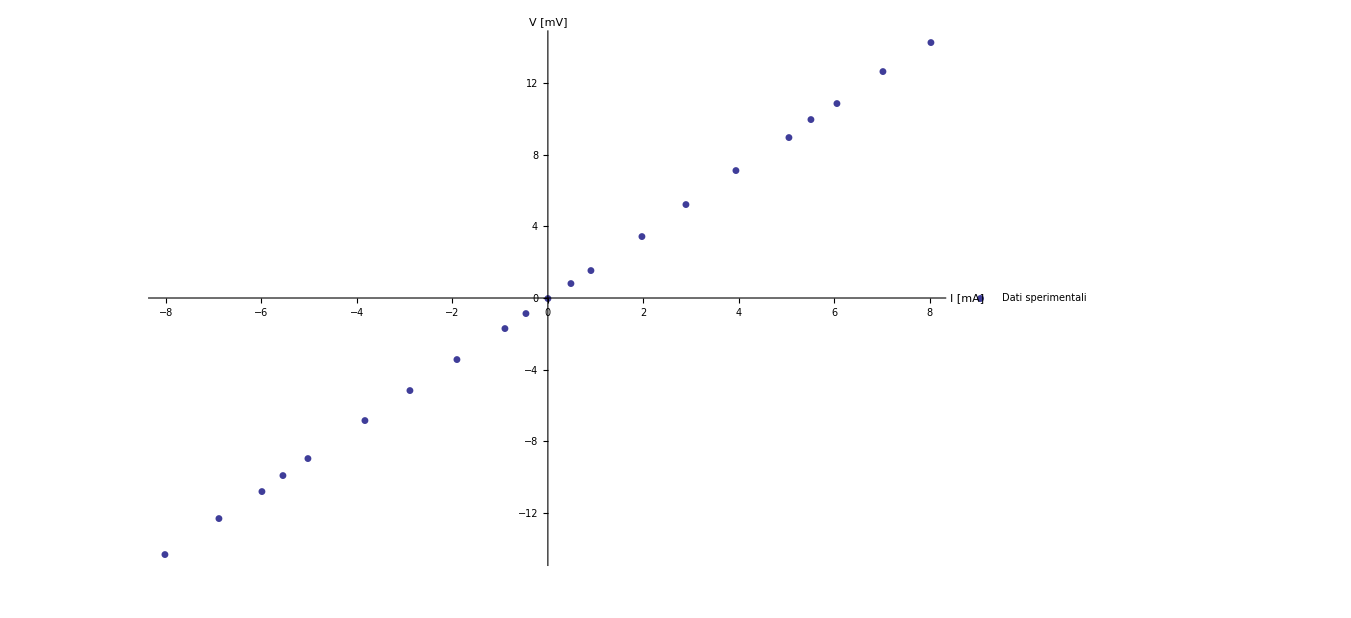

```mathematica
Grafico2=ErrorListPlot[err2,PlotRange->All,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Black,Bold,Large],ImageSize->1000,PlotMarkers->Automatic,PlotLegends->{"Dati sperimentali"}]
```

#### Parametri del fit lineare con il metodo dei minimi quadrati

```mathematica
a2=matA2[[1]];
siga2=Sqrt[matD2inver[[1,1]]];
b2=matA2[[2]];
sigb2=Sqrt[matD2inver[[2,2]]];
f2[x_]:=a1+b1*x;
Print["Retta y = f(x) = a + bx"]
Print["a = (",a2," ± ",siga2,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]]
Print["b = (",b2," ± ",sigb2,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-1,""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-1,""]]]
```

Retta y = f(x) = a + bx

a = (0.0094043 ± 0.0141223)mV

StringJoin::string: String expected at position 2 in "mV" <> 1/"mA".

b = (1.79172 ± 0.00299618)mV<>1/mA

#### Grafico della retta di fit

```mathematica
GraficoRetta2=Plot[f2[x],{x,First[ascissa],Last[ascissa]},PlotRange->All,ImageSize->1000,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Black,Bold,Large],PlotStyle->Red,PlotLegends->{"Best fit"}]
```

-Graphics-

#### Grafico cumulativo (dati e retta)

```mathematica
GraficoTot2=Show[Grafico2,GraficoRetta2]
```

-Graphics-

#### Parametri del Chi Quadro

```mathematica
chi22=Sum[(f2[ascissa[[i]]]-ordinata[[i]])^2/sigmaOrdinataPosteriori[[i]]^2,{i,Lungh}];
sy2=Sqrt[Sum[(f2[ascissa[[i]]]-ordinata[[i]])^2/(Lungh-2),{i,Lungh}]];
Print["Coefficiente di correlazione lineare: ρ = ",Correlation[ascissa,ordinata]," (invariato)"]
Print["χ^2 = ",chi22," (inutile)"]
Print["Gradi di libertà del sistema: dof = ",Lungh-2]
Print["Eventuale errore a posteriori sulle ordinate: σ_y = ",sy1,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]]
```

Coefficiente di correlazione lineare: ρ = 0.999973 (invariato)

χ^2 = 19. (inutile)

Gradi di libertà del sistema: dof = 19

Eventuale errore a posteriori sulle ordinate: σ_y = 0.0647165mV

# Export su file

```mathematica
CreateDirectory[$UserDocumentsDirectory<>"\\"<>NomeEsperienza<>"\\"<>NomeFit];
dir=$UserDocumentsDirectory<>"\\"<>NomeEsperienza<>"\\"<>NomeFit;
```

```mathematica
If[DirectoryQ[dir<>"\\PrimaAnalisi"],primaAnalisi=SetDirectory[dir<>"\\PrimaAnalisi"],primaAnalisi=CreateDirectory[dir<>"\\PrimaAnalisi"]];
If[DirectoryQ[dir<>"\\SecondaAnalisi"],secondaAnalisi=SetDirectory[dir<>"\\SecondaAnalisi"],secondaAnalisi=CreateDirectory[dir<>"\\SecondaAnalisi"]];
If[DirectoryQ[dir<>"\\TerzaAnalisi"],terzaAnalisi=SetDirectory[dir<>"\\TerzaAnalisi"],terzaAnalisi=CreateDirectory[dir<>"\\TerzaAnalisi"]];
SetDirectory[dir];
Print["I file verranno inseriti nelle cartelle corrispondenti al seguente indirizzo: ",dir]
```

I file verranno inseriti nelle cartelle corrispondenti al seguente indirizzo: C:\Users\ricca_000\Documents\EffettoHall\1200mA

#### Export dei contenuti della prima analisi

```mathematica
outputPrimaAnalisi={{,"Analisi dati (errori su ascisse e ordinate)",},{,,},{,"Parametri del fit (y = a + bx)",},{"Parametro","Errore","Unità"},{"a = ",a,siga,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]},{"b = ",b,sigb,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-1)",""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-1)",""]]},{,,},{,"Coefficiente di correlazione lineare",},{"r = ",Correlation[ascissa,ordinata],},{,,},{,"Chi Quadrato",},{"chi = ",chi2,},{,,},{,"Errore a posteriori",},{"sigma = ",sy,},{,,},{,"Gradi di libertà",},{"dof = ",Lungh-2,}};
Export[file1=primaAnalisi<>"\\AnalisiDati1.xls",outputPrimaAnalisi];
Export[graph11=primaAnalisi<>"\\GraficoExp1.png",Grafico];
Export[graph21=primaAnalisi<>"\\GraficoRetta1.png",GraficoRetta];
Export[graph31=primaAnalisi<>"\\GraficoSovrapposto1.png",GraficoTot];
SetDirectory[dir];
If[FileExistsQ[file1],"File salvato in: "<>file1,"Errore: controllare i parametri"]
If[FileExistsQ[graph11],"File salvato in: "<>graph11,"Errore: controllare i parametri"]
If[FileExistsQ[graph21],"File salvato in: "<>graph21,"Errore: controllare i parametri"]
If[FileExistsQ[graph31],"File salvato in: "<>graph31,"Errore: controllare i parametri"]
```

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\PrimaAnalisi\AnalisiDati1.xls

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\PrimaAnalisi\GraficoExp1.png

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\PrimaAnalisi\GraficoRetta1.png

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\PrimaAnalisi\GraficoSovrapposto1.png

#### Export dei contenuti della seconda analisi

```mathematica
outputSecondaAnalisi={{,"Analisi dati (errori solo sulle ordinate)",},{,,},{,"Parametri del fit (y = a + bx)",},{"Parametro","Errore","Unità"},{"a = ",a1,siga1,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]},{"b = ",b1,sigb1,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-1)",""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-1)",""]]},{,,},{,"Coefficiente di correlazione lineare",},{"r = ",Correlation[ascissa,ordinata],},{,,},{,"Chi Quadrato",},{"chi = ",chi21,},{,,},{,"Errore a posteriori",},{"sigma = ",sy1,},{,,},{,"Gradi di libertà",},{"dof = ",Lungh-2,}};
Export[file2=secondaAnalisi<>"\\AnalisiDati2.xls",outputSecondaAnalisi];
Export[graph12=secondaAnalisi<>"\\GraficoExp2.png",Grafico1];
Export[graph22=secondaAnalisi<>"\\GraficoRetta2.png",GraficoRetta1];
Export[graph32=secondaAnalisi<>"\\GraficoSovrapposto2.png",GraficoTot1];
SetDirectory[dir];
If[FileExistsQ[file2],"File salvato in: "<>file2,"Errore: controllare i parametri"]
If[FileExistsQ[graph12],"File salvato in: "<>graph12,"Errore: controllare i parametri"]
If[FileExistsQ[graph22],"File salvato in: "<>graph22,"Errore: controllare i parametri"]
If[FileExistsQ[graph32],"File salvato in: "<>graph32,"Errore: controllare i parametri"]
```

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\SecondaAnalisi\AnalisiDati2.xls

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\SecondaAnalisi\GraficoExp2.png

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\SecondaAnalisi\GraficoRetta2.png

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\SecondaAnalisi\GraficoSovrapposto2.png

#### Export dei contenuti della terza analisi

```mathematica
outputTerzaAnalisi={{,"Analisi dati (errore a posteriori)",},{,,},{,"Parametri del fit (y = a + bx)",},{"Parametro","Errore","Unità"},{"a = ",a2,siga2,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]},{"b = ",b2,sigb2,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-1)",""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-1)",""]]},{,,},{,"Coefficiente di correlazione lineare",},{"r = ",Correlation[ascissa,ordinata],},{,,},{,"Chi Quadrato",},{"chi = ",chi22,},{,,},{,"Errore a posteriori",},{"sigma = ",sy2,},{,,},{,"Gradi di libertà",},{"dof = ",Lungh-2,}};
Export[file3=terzaAnalisi<>"\\AnalisiDati3.xls",outputTerzaAnalisi];
Export[graph13=terzaAnalisi<>"\\GraficoExp3.png",Grafico2];
Export[graph23=terzaAnalisi<>"\\GraficoRetta3.png",GraficoRetta2];
Export[graph33=terzaAnalisi<>"\\GraficoSovrapposto3.png",GraficoTot2];
SetDirectory[dir];
If[FileExistsQ[file3],"File salvato in: "<>file3,"Errore: controllare i parametri"]
If[FileExistsQ[graph13],"File salvato in: "<>graph13,"Errore: controllare i parametri"]
If[FileExistsQ[graph23],"File salvato in: "<>graph23,"Errore: controllare i parametri"]
If[FileExistsQ[graph33],"File salvato in: "<>graph33,"Errore: controllare i parametri"]
```

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\TerzaAnalisi\AnalisiDati3.xls

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\TerzaAnalisi\GraficoExp3.png

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\TerzaAnalisi\GraficoRetta3.png

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\1200mA\TerzaAnalisi\GraficoSovrapposto3.png